```mathematica
k=200;
```

```mathematica
costfunction[board_,weight_]:=Module[{team1,team2,zeroes,cost,me,min1,min2,cf},
(*team1=Position[board,1];
team2=Position[board,2];
zeroes=Position[board,0];
cf=Table[
me=PS[[jj]];
If[Length[team1]>0,
min1=Min[Table[Norm[me-team1[[m]]],{m,1,Length[team1]}]];
,
min1=0
];
If[Length[team2]>0,
min2=Min[Table[Norm[me-team2[[m]]],{m,1,Length[team2]}]];
,
min2=0
];
If[min1<min2,weight[[me[[1]]]][[me[[2]]]],If[min1>min2,-weight[[me[[1]]]][[me[[2]]]],0.]]
,{jj,1,Length[PS]}];
Return[Total[cf]];*)
COMPUTER=Position[board,1];
HUMAN=Position[board,2];
PTS=Nearest[Position[board,_?(#>0&)]];
cf=Total[Flatten[Table[
Table[
near=PTS[{i,j}];
If[Length[near]==2,
0,
near=near[[1]];
If[MemberQ[COMPUTER,near]==True,
-weight[[near[[1]],near[[2]]]]
,
weight[[near[[1]],near[[2]]]]
]
]
,{j,1,10}]
,{i,1,10}]]];
Return[cf];
]
```

```mathematica
GenBoards[board_,weight_,team_]:=Module[{boardtmp,options,moveoptions,set,set2},
options=Position[board,0];
If[team==1,set=1;set2=2;,set=2;set2=1;];
moveoptions=Table[
boardtmp=board;
boardtmp[[options[[i]][[1]]]][[options[[i]][[2]]]]=set;
boardtmp
,{i,1,Length[options]}];
Return[moveoptions];
]
```

### YOU GO FIRST

### Monte Carlo Tree Search

```mathematica
grid=10;
TotalArea= grid^2;
board=Table[0,{grid},{grid}];
PS=Position[board,0];
weight=Table[(*i j*)1,{i,1,grid},{j,1,grid}];
```

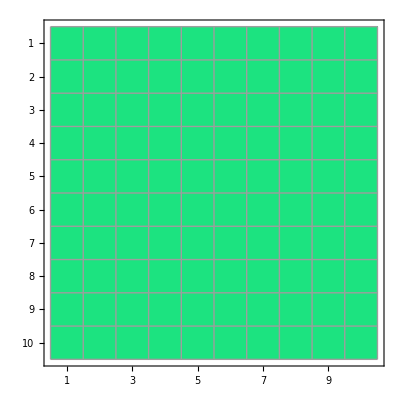

```mathematica
MatrixPlot[weight,ColorFunction->"TemperatureMap",Mesh->All,ColorRules->{1->RGBColor[0.11,0.89,0.5]},FrameStyle->Black]
```

### Your Move

```mathematica
board[[5]][[5]]=2;
```

### My Move

```mathematica
allboards=GenBoards[board,weight,1];
```

```mathematica
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;7]];
Table[tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;,{i,1,4}];
Table[tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;,{i,5,7}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
```

```mathematica
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
```

```mathematica
tc=Flatten[board];
```

```mathematica
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
```

```mathematica
froplot=Partition[toplot,grid];
```

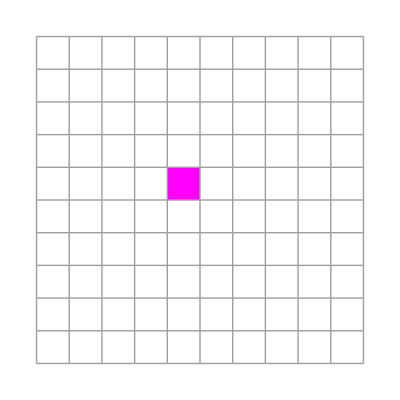

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Black,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
```

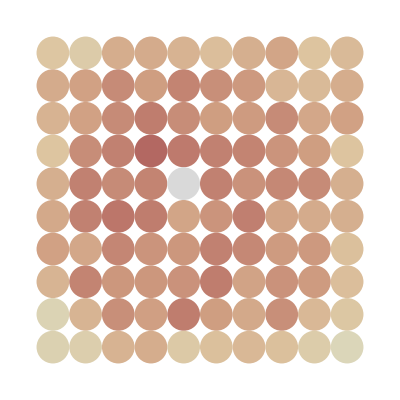

```mathematica
Graphics[plotme]
```

```mathematica
bestboard=Position[byplace,Max[byplace]][[1]][[1]];

board=allboards[[bestboard]];
```

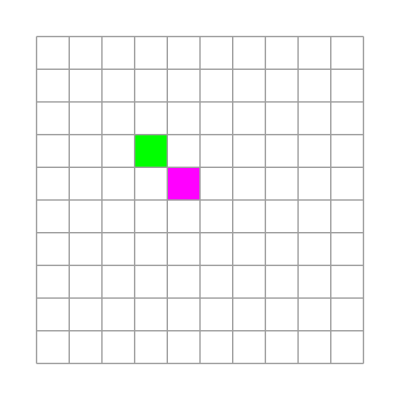

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
costfunction[board,weight]
```

-36.

### Your Move

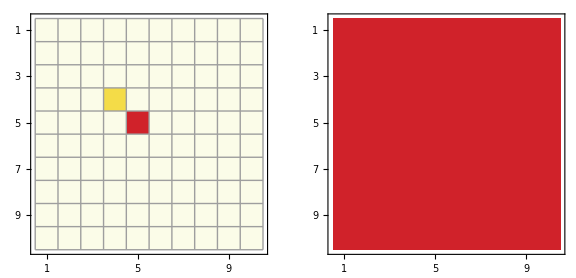

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
board[[7]][[6]]
```

0

```mathematica
board[[7]][[6]]=2
```

2

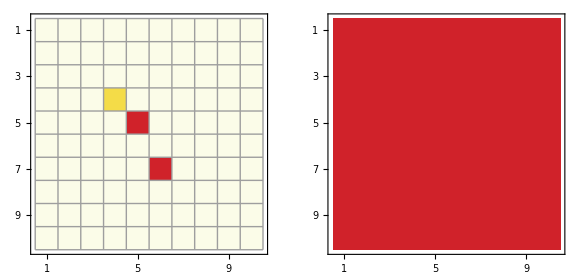

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

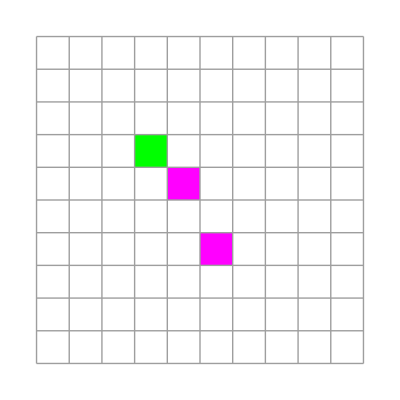

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

### My Move

```mathematica
allboards=GenBoards[board,weight,1];
```

```mathematica
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;5]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,3}];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;
,{i,4,5}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
```

```mathematica
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
```

```mathematica
tc=Flatten[board];
```

```mathematica
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
```

```mathematica
froplot=Partition[toplot,grid];
```

```mathematica
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Green,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
```

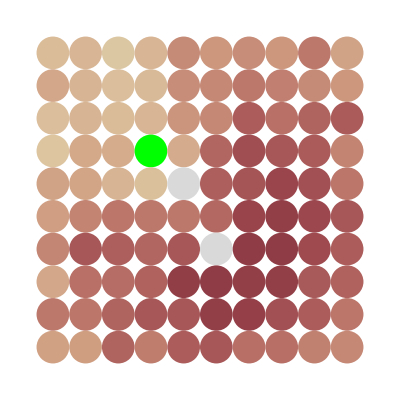

```mathematica
Graphics[plotme]
```

```mathematica
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
```

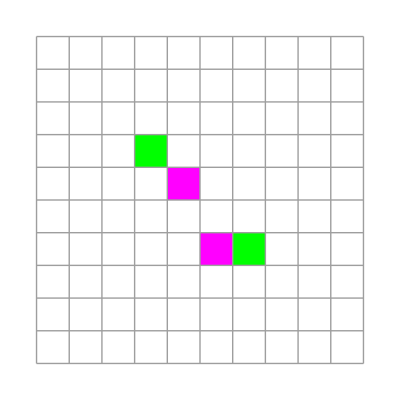

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
costfunction[board,weight]
```

20.

### Your Move

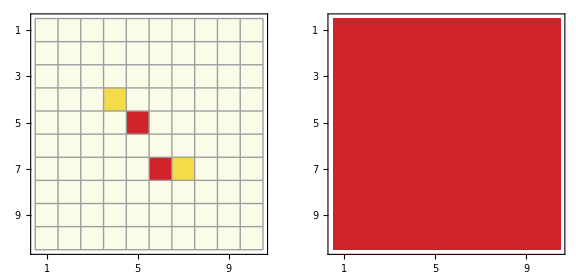

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
board[[4]][[7]]
```

0

```mathematica
board[[4]][[7]]=2
```

2

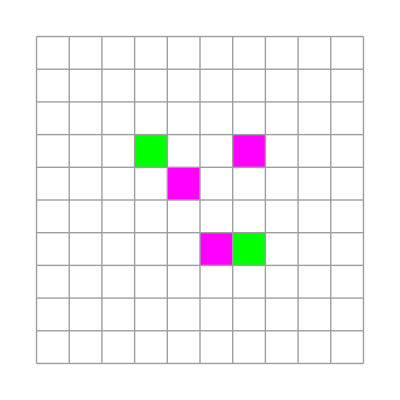

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

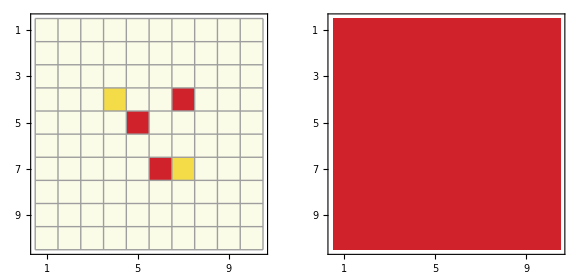

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

### My Move

```mathematica
allboards=GenBoards[board,weight,1];
```

```mathematica
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;3]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,2}];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=2;
,{i,3,3}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
```

```mathematica
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
```

```mathematica
tc=Flatten[board];
```

```mathematica
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
```

```mathematica
froplot=Partition[toplot,grid];
```

```mathematica
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Black,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
```

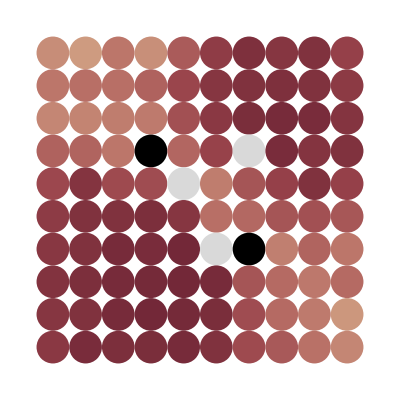

```mathematica
Graphics[plotme]
```

```mathematica
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
```

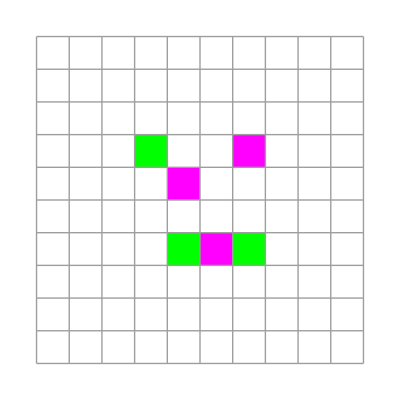

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
costfunction[board,weight]
```

33.

### Your Move

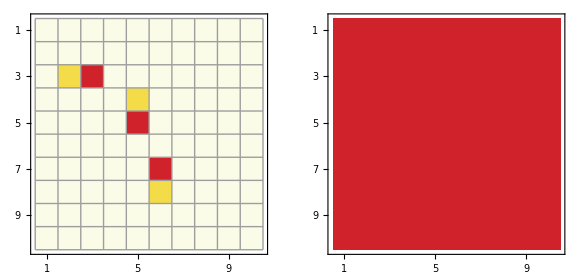

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

```mathematica
board[[4]][[8]]
```

0

```mathematica
board[[4]][[8]]=2
```

2

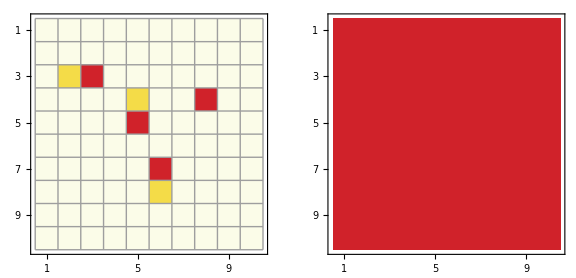

```mathematica
GraphicsRow[
{MatrixPlot[board,ColorFunction->"TemperatureMap",Mesh->All],MatrixPlot[weight,ColorFunction->"TemperatureMap"]}
,ImageSize->Large]
```

### My Move

```mathematica
allboards=GenBoards[board,weight,1];
```

```mathematica
byplace=ParallelTable[
percent=Table[
tmp=allboards[[j]];
moves=RandomSample[Position[tmp,0]][[;;1]];
Table[
tmp[[moves[[i]][[1]]]][[moves[[i]][[2]]]]=1;
,{i,1,1}];
If[costfunction[tmp,weight]>0,1,0]
,{k}];
1.Total[percent]/k
,{j,1,Length[allboards]}];
```

```mathematica
Table[If[byplace[[i]]==1,byplace[[i]]=1.1],{i,1,Length[byplace]}];
```

```mathematica
tc=Flatten[board];
```

```mathematica
mn=0;
toplot=Table[If[tc[[i]]==0,mn++;byplace[[mn]],tc[[i]]],{i,1,Length[tc]}];
```

```mathematica
froplot=Partition[toplot,grid];
```

```mathematica
plotme=Table[
Table[
If[froplot[[j]][[i]]==1,{Black,Disk[{i,grid-j},0.5]},
If[froplot[[j]][[i]]==2,{LightGray,Disk[{i,grid-j},0.5]},
{ColorData[{"RedBlueTones","Reverse"}][froplot[[j]][[i]]],Disk[{i,grid-j},0.5]}
]
]
,{i,1,Length[froplot]}]
,{j,1,Length[froplot]}];
```

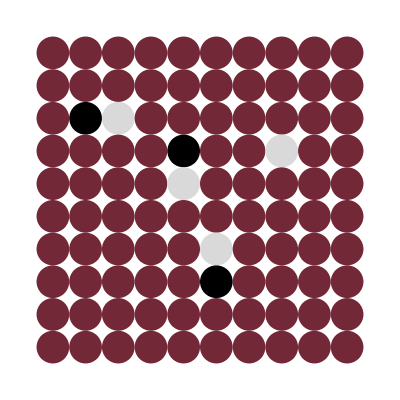

```mathematica
Graphics[plotme]
```

```mathematica
bestboard=Position[byplace,Max[byplace]][[1]][[1]];
board=allboards[[bestboard]];
```

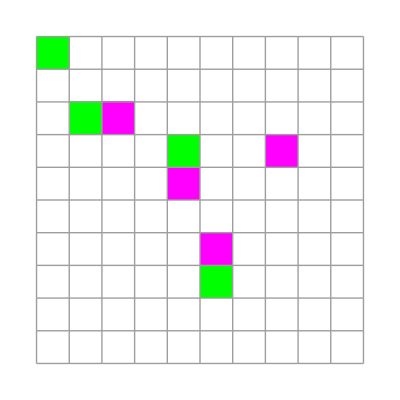

```mathematica
ArrayPlot[board,ColorRules->{1->Green,2->Magenta},Mesh->True,PlotRangePadding->0]
```

```mathematica
finalscore=costfunction[board,weight];
```

```mathematica
If[finalscore>0,Print[Style["MACHINE>MAN",Black,100]],Print[Style["MAN>MACHINE",Black,100]];
]
```

MACHINE>MAN

```mathematica
finalscore
```

1.